```mathematica
Solve[{r==b-d,AI/PI==d/b},{b,d}]//FullSimplify
```

{{b→(PI r)/(-AI+PI),d→(AI r)/(-AI+PI)}}

```mathematica
(*beta[x_ ?NumberQ, n_ ?NumberQ] := Max[(1-x/2)^2/(1-n/2)^2+ 1*^-8, 1]*)
```

```mathematica
beta[x_, η_] := 1-1/(η + E^(Abs[x-2]^0.5))
```

```mathematica
beta[2,0.001]
```

0.999001

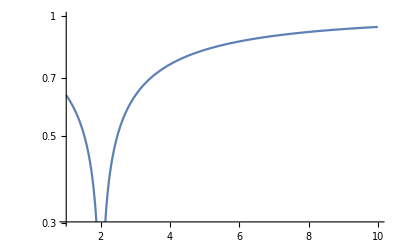

```mathematica
LogPlot[beta[x,0.00001], {x,1,10}]
```

```mathematica
myfun[λ_,δ_?NumberQ,n_?NumberQ, η_ ?NumberQ]:=Eigenvalues[Table[If[i==j, λ(2(1-beta[j, η])^i-1)-δ,If[2j≥i>j,λ Binomial[j,i-j] beta[j, η]^(i-j)(1-beta[j, η])^(2j-i),If[j>i,λ Binomial[j,j-i] beta[j, η]^(j-i)(1-beta[j, η])^i,0]]],{i,n},{j,n}],
1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]]
```

```mathematica
critDelta[δ_?NumberQ, n_?NumberQ]:=η/.FindRoot[myfun[1,δ,n,η]==0,{η,0.9999,0,100}];
```

```mathematica
nvals={3,5,10,20};
leg="n = "<>ToString[#]&/@nvals;
colorList=ColorData[37,"ColorList"];
```

```mathematica
(*critTable=Table[{δ,critDelta[δ,#]},{δ,0.0,1,0.1}]&/@nvals;*)
critTable=Table[{δ,beta[#/2,critDelta[δ,#]]},{δ,0.0,1,0.1}]&/@nvals;
(*critTable2=Table[{δ,critDelta[δ,#]},{δ,1-1*^-3+1*^-5,1-1*^-5,1*^-5}]&/@nvals;*)
```

```mathematica
critTable
```

{{{0.,0.76985},{0.1,0.730735},{0.2,0.691186},{0.3,0.653},{0.4,0.618275},{0.5,0.588652},{0.6,0.564582},{0.7,0.545412},{0.8,0.530049},{0.9,0.517479},{1.,0.506931}},{{0.,0.830992},{0.1,0.786753},{0.2,0.739684},{0.3,0.691888},{0.4,0.646412},{0.5,0.606706},{0.6,0.574918},{0.7,0.550771},{0.8,0.532516},{0.9,0.518345},{1.,0.506931}},{{0.,0.92275},{0.1,0.901376},{0.2,0.88182},{0.3,0.865083},{0.4,0.851586},{0.5,0.841453},{0.6,0.834445},{0.7,0.829848},{0.8,0.826801},{0.9,0.824669},{1.,0.823079}},{{0.,0.965375},{0.1,0.957224},{0.2,0.95145},{0.3,0.947569},{0.4,0.945003},{0.5,0.943345},{0.6,0.942321},{0.7,0.941708},{0.8,0.941329},{0.9,0.941077},{1.,0.940894}}}

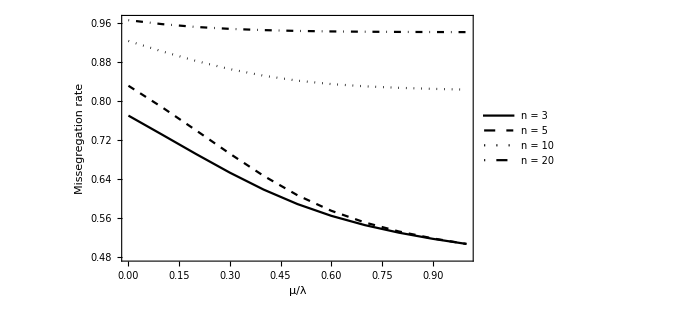

```mathematica
ListPlot[#&/@critTable,
Joined->True,
Frame->True,
Axes->False,
PlotRange->{All,All},
(*Epilog->points,*)
PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}},
FrameLabel->{"μ/λ","Missegregation rate"},
FrameStyle->Directive[Thickness[0.0035],Black],
LabelStyle->{FontSize->18,Black,FontFamily->"Arial"},
PlotLegends->leg,
ImageSize->500
]
```

```mathematica
ListPlot[nvals,Joined->True,Frame->True,Axes->False,PlotRange->{All,All},PlotStyle->{{GrayLevel[0]},{GrayLevel[0],Dashing[{Small,Small}]},{GrayLevel[0],Dashing[{0,Small}]},{GrayLevel[0],Dashing[{0,Small,Small,Small}]}},FrameLabel->{"μ/λ","Missegregation rate"},FrameStyle->Directive[Thickness[0.0035],GrayLevel[0]],LabelStyle->{FontSize->18,GrayLevel[0],FontFamily->"Arial"},PlotLegends->leg,ImageSize->500]
```

ListPlot::lpn: nvals is not a list of numbers or pairs of numbers.

ListPlot[nvals,Joined→True,Frame→True,Axes→False,PlotRange→{All,All},PlotStyle→{{GrayLevel[0]},{GrayLevel[0],Dashing[{Small,Small}]},{GrayLevel[0],Dashing[{0,Small}]},{GrayLevel[0],Dashing[{0,Small,Small,Small}]}},FrameLabel→{μ/λ,Missegregation rate},FrameStyle→Directive[Thickness[0.0035],GrayLevel[0]],LabelStyle→{FontSize→18,GrayLevel[0],FontFamily→Arial},PlotLegends→leg,ImageSize→500]

```mathematica
With[{n=5},Table[If[i==j, λ(1-2μ)-δ,If[Abs[i-j]==1,λ μ,0]],{i,n},{j,n}]]//MatrixForm
```

(-δ+λ (1-2 μ) | λ μ | 0 | 0 | 0
λ μ | -δ+λ (1-2 μ) | λ μ | 0 | 0
0 | λ μ | -δ+λ (1-2 μ) | λ μ | 0
0 | 0 | λ μ | -δ+λ (1-2 μ) | λ μ
0 | 0 | 0 | λ μ | -δ+λ (1-2 μ))

```mathematica
list={{0.96354,0.01},{0.256,0.01},{0.9874,0.01},{0.9834,0.01},{0.9754,0.01},{0.992,0.01},{0.9496,0.01},{0.9344,0.01},{0.6349,0.01}};
```

```mathematica
points=Flatten[{PointSize[0.015],colorList[[#]],Point[{list[[#,1]],list[[#,2]]}]}&/@Range[Length[list]],1]
```

{PointSize[0.015],RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],Point[{0.96354,0.01}],PointSize[0.015],RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],Point[{0.256,0.01}],PointSize[0.015],RGBColor[1., 0.5568627450980392, 0.3215686274509804],Point[{0.9874,0.01}],PointSize[0.015],RGBColor[1., 0.807843137254902, 0.4627450980392157],Point[{0.9834,0.01}],PointSize[0.015],RGBColor[0.8156862745098039, 0.6078431372549019, 0.23137254901960785],Point[{0.9754,0.01}],PointSize[0.015],RGBColor[0.6588235294117647, 0.596078431372549, 0.27058823529411763],Point[{0.992,0.01}],PointSize[0.015],RGBColor[0.9294117647058824, 0.9058823529411765, 0.7803921568627451],Point[{0.9496,0.01}],PointSize[0.015],RGBColor[0.8117647058823529, 0.7607843137254902, 0.47843137254901963],Point[{0.9344,0.01}],PointSize[0.015],RGBColor[0.6588235294117647, 0.7803921568627451, 0.9411764705882353],Point[{0.6349,0.01}]}

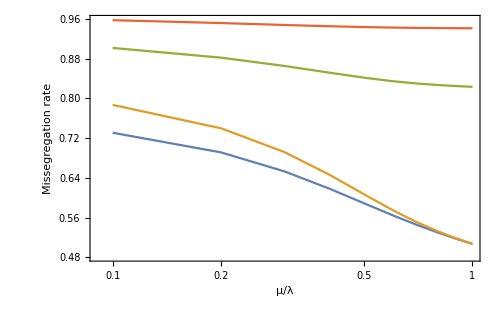

```mathematica
ListLogLinearPlot[critTable,
Joined->True,
Frame->True,
Axes->False,
PlotRange->All,
Epilog->points,
FrameLabel->{"μ/λ","Missegregation rate"},
FrameStyle->Directive[Thickness[0.0035],Black],
LabelStyle->{FontSize->18,Black,FontFamily->"Arial"},
ImageSize->500
]
```

```mathematica
makeErrors[med_,low_,high_]:=Around[med,{med-low,high-med}];
makeErrorsReverse[med_,low_,high_]:=Around[med,{high-med,med-low}];
```

```mathematica
birthList={{0.192,0.015,1.667},{0.207,0.018,0.625},{0.239,0.019,1.111},{0.303,0.179,0.417},{0.122,0.021,0.556},{0.25,0.159,0.323},{0.139,0.024,0.286},{0.122,0.036,0.667},{0.063,0.043,0.4}};
growthList={{0.007,0.003,0.033},{0.154,0.035,0.347},{0.003,0.0003,0.038},{0.005,0.0004,0.013},{0.003,0.0003,0.016},{0.002,0.0004,0.012},{0.007,0.002,0.014},{0.008,0.005,0.013},{0.023,0.01,0.5}};
```

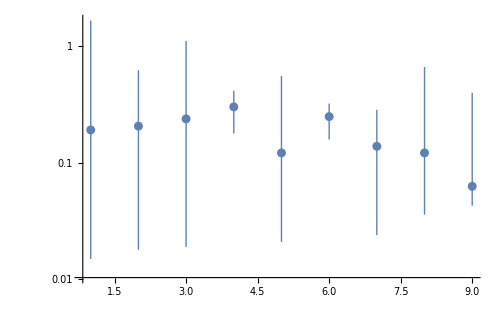

```mathematica
ListLogPlot[makeErrors@@#&/@birthList,
Ticks->{{},Automatic},
PlotRange->All,
ImageSize->500]
```

```mathematica
makeErrors@@#&/@birthList
```

{0.190.181.5,0.210.190.4,0.240.220.9,0.300.120.11,0.120.100.4,0.250.090.07,0.140.120.15,0.120.090.5,0.0630.0200.34}

```mathematica
labels={"Head and neck","Esophogaeal","Colorectal","Rectal","Breast","Cervix","Melanoma","SC Lung","D-LBCL"};
```

```mathematica
Legended[PairedBarChart[makeErrors@@#&/@birthList,makeErrors@@#&/@growthList,
ChartStyle->ColorData[11,"ColorList"],
FrameLabel->{"A","B"},
PlotRange->All]
,Placed[
SwatchLegend[
colorList,
labels,
LabelStyle->{Black,FontSize->16,FontFamily->"Arial"},
LegendMarkers->"Bubble",
LegendLayout->"Row"
]
,
Top]
]
```

-Graphics-

```mathematica
PairedBarChart[makeErrors@@#&/@birthList,makeErrors@@#&/@growthList,
ChartStyle->colorList,
BarSpacing->{5,0,0.5},
ChartLabels->labels,
PlotRange->All,
ImageSize->500,
ScalingFunctions->"Log",
FrameStyle->Directive[Thickness[0.0035],Black],
LabelStyle->{FontSize->18,Black,FontFamily->"Arial"},
Ticks->{{0.001,0.01,0.1},{}}]
```

-Graphics-

```mathematica
ColorData[37,"ColorList"]
```

{RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],RGBColor[1., 0.5568627450980392, 0.3215686274509804],RGBColor[1., 0.807843137254902, 0.4627450980392157],RGBColor[0.8156862745098039, 0.6078431372549019, 0.23137254901960785],RGBColor[0.6588235294117647, 0.596078431372549, 0.27058823529411763],RGBColor[0.9294117647058824, 0.9058823529411765, 0.7803921568627451],RGBColor[0.8117647058823529, 0.7607843137254902, 0.47843137254901963],RGBColor[0.6588235294117647, 0.7803921568627451, 0.9411764705882353],RGBColor[0.4235294117647059, 0.6039215686274509, 0.8431372549019608],RGBColor[0.2, 0.41568627450980394, 0.7019607843137254]}

```mathematica
myleg=SwatchLegend[
colorList,
labels,
LabelStyle->{Black,FontSize->16,FontFamily->"Arial"},
LegendMarkers->"Bubble",
LegendLayout->{"Row",3},
LegendFunction->"Frame"
]
```

```mathematica
Export[NotebookDirectory[]<>"../../legend_3Rows.pdf",myleg];
```

```mathematica
{μx,σx} ={0.192, (1.667-0.015)/4};
{μy,σy} ={0.007, (0.033-0.003)/4};
{μ,σ}={Log[μx^2/(√(μx^2+σx^2))],Log[1+σx^2/μx^2]}
```

{-2.51405,1.72757}

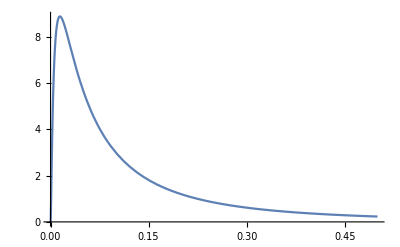

```mathematica
Plot[PDF[LogNormalDistribution[-2.514,1.314],x],{x,0,0.5},PlotRange->All]
```

```mathematica
Mean[LogNormalDistribution[a,b]]
StandardDeviation[LogNormalDistribution[a,b]]
```

ⅇ^(a+b^2/2)

√(ⅇ^(2 a+b^2) (-1+ⅇ^(b^2)))

```mathematica
NSolve[{a+b^2/2==Log[μy],(2a+b^2)+Log[-1+ⅇ^(b^2)]==2Log[σy],b>0},{a,b}][[1]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{a→-5.3441,b→0.874367}

```mathematica
lognormal[μ_,min_,max_]:=Module[
{soln,σ},
σ=(max-min)/4;
soln =Quiet@ NSolve[{a+b^2/2==Log[μ],(2a+b^2)+Log[-1+ⅇ^(b^2)]==2Log[σ],b>0},{a,b}][[1]];
{a,b}/.soln
]
```

```mathematica
birth=lognormal@@#&/@birthList
netgrowth=lognormal@@#&/@growthList
```

{{-2.51405,1.31437},{-1.79009,0.655826},{-1.84878,0.91377},{-1.21294,0.194515},{-2.49839,0.888437},{-1.39956,0.162913},{-2.07355,0.447807},{-2.59514,0.991364},{-3.31508,1.04925}}

{{-5.3441,0.874367},{-1.98498,0.477869},{-7.00215,1.54467},{-5.46545,0.578148},{-6.30794,0.998794},{-6.78071,1.06405},{-5.04616,0.410637},{-4.85863,0.246221},{-5.4622,1.83844}}

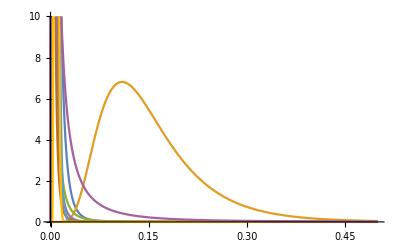

```mathematica
Plot[Evaluate[PDF[LogNormalDistribution@@#,x]&/@netgrowth],{x,0,0.5},PlotRange->{All,{0,10}}]
```

```mathematica
drawRatio[bparams_,rparams_]:=Module[
{},
Max[0,1-RandomVariate[LogNormalDistribution@@rparams]/RandomVariate[LogNormalDistribution@@bparams]]
]
```

```mathematica
randData=Table[drawRatio[birth[[n]],netgrowth[[n]]]&/@Range[200],{n,1,Length[birth]}];
```

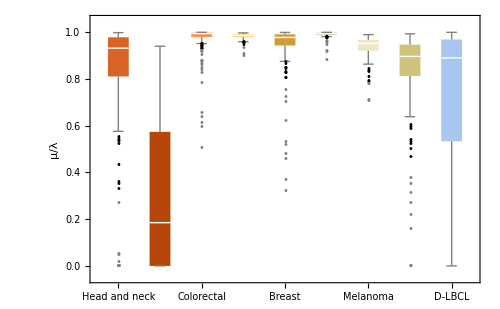

```mathematica
BoxWhiskerChart[randData,"Outliers",
ChartStyle->colorList,
BarSpacing->Large,
ChartLabels->Placed[labels,Axis,Rotate[#,π/4]&],
FrameLabel->{"","μ/λ"},
FrameStyle->Directive[Thickness[0.0035],Black],
LabelStyle->{FontSize->14,Black,FontFamily->"Arial"},
ImageSize->500]
```

```mathematica
data = Import[NotebookDirectory[]<>"Predicted_LaggingChrPct_TCGA.txt","Data"]
```

Import::nffil: File /Users/80019141/Repositories/ploidyEvolution/Mathematica/Predicted_LaggingChrPct_TCGA.txt not found during Import.

$Failed

```mathematica
header=data[[1]];
rawdata=data[[2;;,All]];
```

```mathematica
Position[rawdata[[All,1]],s_String/;StringMatchQ[s,"brca*",IgnoreCase->True]]//Flatten;
```

```mathematica
rawdata[[1101,1]]
```

HNSC.TCGA-4P-AA8J-01A-11R-A39I-07

```mathematica
cancerTypes =DeleteDuplicates[StringTake[rawdata[[All,1]],4]]
```

{BRCA,HNSC,COAD,ESCA,READ,CESC,SKCM,LUSC,DLBC}

```mathematica
locations=Flatten[Position[rawdata[[All,1]],s_String/;StringMatchQ[s,#<>"*",IgnoreCase->True]]]&/@cancerTypes;
```

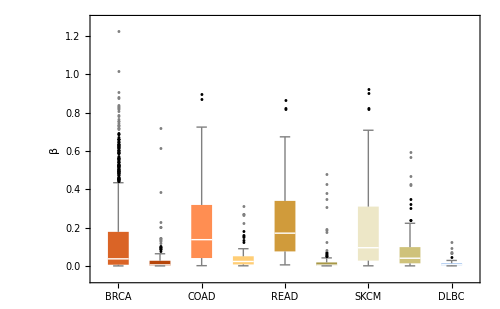

```mathematica
BoxWhiskerChart[rawdata[[#,3]]/100&/@locations,"Outliers",
ChartStyle->colorList,
BarSpacing->Large,
ChartLabels->Placed[cancerTypes,Axis,Rotate[#,π/4]&],
FrameLabel->{"","β"},
FrameStyle->Directive[Thickness[0.0035],Black],
LabelStyle->{FontSize->14,Black,FontFamily->"Arial"},
ImageSize->500]
```

```mathematica
labels
```

{Head and neck,Esophogaeal,Colorectal,Rectal,Breast,Cervix,Melanoma,SC Lung,D-LBCL}

```mathematica
DiscretePlot[rawdata[[#,3]]/100&/@locations]
```

DiscretePlot::argr: DiscretePlot called with 1 argument; 2 arguments are expected.

```mathematica
leg2="n_"<>ToString[#]&/@nvals;
```

```mathematica
Export[NotebookDirectory[]<>"criticalcurve_"<>ToString[leg2[[#]]]<>".csv",critTable[[#]],"CSV"]&/@Range[4]
```

{/Users/80019141/Repositories/ploidyEvolution/Mathematica/criticalcurve_n_3.csv,/Users/80019141/Repositories/ploidyEvolution/Mathematica/criticalcurve_n_5.csv,/Users/80019141/Repositories/ploidyEvolution/Mathematica/criticalcurve_n_10.csv,/Users/80019141/Repositories/ploidyEvolution/Mathematica/criticalcurve_n_20.csv}

```mathematica
leg2
```

{n_5,n_10,n_20,n_40}

```mathematica
critTable2=Table[{δ,critDelta[δ,#]},{δ,1-1*^-3,1-1*^-5,2*^-5}]&/@nvals;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
critTable2;
```

```mathematica
Log[critTable2[[All,-1]]]
```

{{-Log[50000/49999],-10.337},{-Log[50000/49999],-9.72489},{-Log[50000/49999],-9.07692},{-Log[50000/49999],-8.40943}}

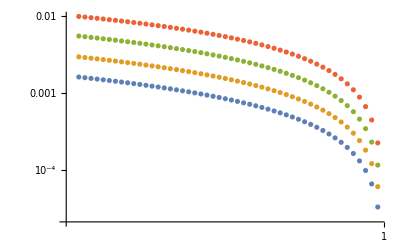

```mathematica
ListLogLogPlot[critTable2]
```